```mathematica
ComplexQ = # ∈ Complexes &;
RealQ=#∈Reals &;
ProbabilityCoefQ = #∈Reals ∧ 0≤ #≤ 1 &; 
RealLessThanOneQ=#∈Reals ∧#<1 &;
PositiveQ=#∈Reals ∧#>0&;
```

```mathematica
The definitions of P according to proposition 1:
```

Syntax::sntxf: "The definitions of P according to proposition " cannot be followed by "1:".

```mathematica
P[p_List,0,0] := 1
P[p_List, n_Integer, 0] :=P[p,n,0]=
 1-∑_(m=0)^(n-1) (Binomial[n,m]* P[p,m,n-m])
P[p_List,nt_Integer,nf_Integer]:=P[p,nt,nf] =
P[p, nt,0]∏_(i=0)^nt (1-p⟦i+1⟧)^(nf *Binomial[nt,i])
```

```mathematica
Test on symbolic values. c.f. Example 1:
```

Syntax::sntxf: "Test on symbolic values. c.f. Example 1" cannot be followed by ":".

```mathematica
With[{p= {p0,p1,p2}},
{P[p,0,3],P[p,1,2],P[p,2,0],P[p,2,1]} // FullSimplify 
] // Column
```

(1-p0)^3
(-1+p0)^2 p0 (-1+p1)^2
p0 (p0+2 p1-2 p0 p1)
-(-1+p0) p0 (-1+p1)^2 (-p0+2 (-1+p0) p1) (-1+p2)

```mathematica
The following provides solutions for an equation at individual iteration.
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
EquationSolutions[pg_List,pr_List]:=Module[
{solutions,equation, n=Length[pg]-1,nt=Length[pr]},
ClearAll[p];
equation = pg⟦nt+1⟧==P[Append[pr,p],nt,n-nt];
solutions = Solve[equation,p];
If[solutions === {},
Null,
DeleteDuplicates[p/. solutions]
]
]
```

```mathematica
Test on values from Example 1:
```

Syntax::sntxf: "Test on values from Example 1" cannot be followed by ":".

```mathematica
With[{pg={1/27,8/27,1/54,1/54}},
Column[{
EquationSolutions[pg,{}],
EquationSolutions[pg,{2/3}],
EquationSolutions[pg,{2/3,-1}] == Null
}
]
]
```

{2/3,1/6 (7-ⅈ √3),1/6 (7+ⅈ √3)}
{-1,3}
True

```mathematica
The implementation of the find_PLP algorithm  itself:
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
FindPLP[pg_List, domainQ_, prAccum_List] := Module[{solutions,selected,plp},
If[Length[prAccum] == Length[pg]-1,
prAccum,

solutions = EquationSolutions[pg,prAccum];
If[solutions===Null,
Null,
solutions =  Select[solutions,domainQ];
While[solutions ≠ {},
selected =solutions⟦1⟧;
plp=FindPLP[pg, domainQ,Append[prAccum, selected]];
If[ListQ[plp],
Return[plp],
solutions = Delete[solutions,1]
]];
Null
]
]
]
FindPLP[pg_List, domainQ_]:=FindPLP[pg,domainQ,{}]
Representable[pg_List,domainQ_]:=ListQ[FindPLP[pg,domainQ]]
```

Test reproducing the complete result from Example 1:

```mathematica
Representable[{1/27,8/27,1/54,1/54}, RealLessThanOneQ] 
Representable[{1/27,8/27,1/54,1/54}, RealQ] 
FindPLP[{1/27,8/27,1/54,1/54}, RealQ]
```

False

True

{2/3,3,127/128}

```mathematica
{2/3,3,127/128}s
```

{(2 s)/3,3 s,(127 s)/128}

```mathematica
FindPLP[{0.1,0.2,0.7,0.1}, ComplexQ]
```

{0.535841,-0.316226,-5.70519}

```mathematica
FindPLP[RandomVariate[DirichletDistribution[{1,1,1}]],PositiveQ]
```

{0.824615}

```mathematica
gran=1/100
simplex2=Table[{p0,1-p0},{p0,0,1,gran}];
simplex3=Flatten[Table[{p0,p1,1-p0-p1},{p0,0,1,gran},{p1,0,1-p0,gran}],1];
simplex4=Flatten[Table[{p0,p1,p2,1-p0-p1-p2},{p0,0,1,1/25},{p1,0,1-p0,1/25},{p2,0,1-p0-p1,1/25}],2];
```

1/100

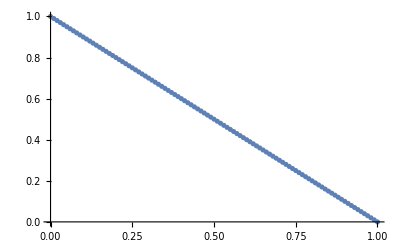

```mathematica
rep2 = Select[simplex2, Representable[#,ProbabilityCoefQ]&];
ListPlot[{rep2}]
```

```mathematica
Unimodal[seq_] := With[{d=Differences[seq]},
AllTrue[
Drop[d, Length[TakeWhile[d,#>0&]]],
#<0&
]
]
P2[l_] := Take[#,2]&/@ l
P3[l_] := Take[#,3]&/@ l
H[b_,x_] :=  - ReleaseHold[Dot[x, Hold[Log[b,#]]&/@x]]
```

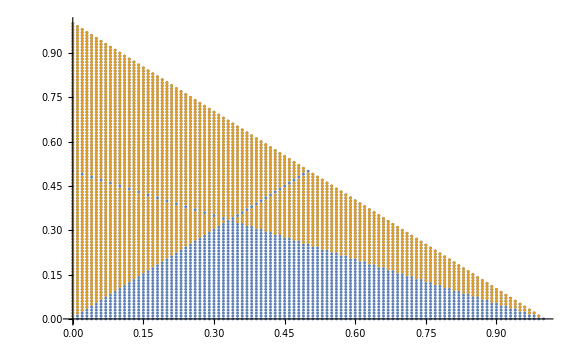
-Graphics3D--Graphics-

```mathematica
unimodal = Select[simplex3, Unimodal];
Row[{ListPointPlot3D[{simplex3,unimodal},ImageSize->Large],ListPlot[{P2[simplex3],P2[unimodal]},ImageSize->Large]}]
```

```mathematica
rep3 = Select[simplex3, Representable[#,ProbabilityCoefQ]&];
```

{{0,0,1},{1,0,0}}

-Graphics3D--Graphics3D-

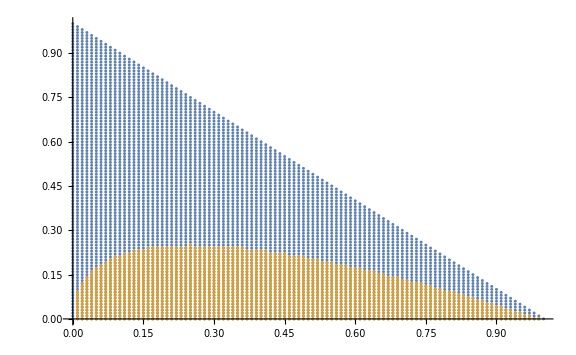
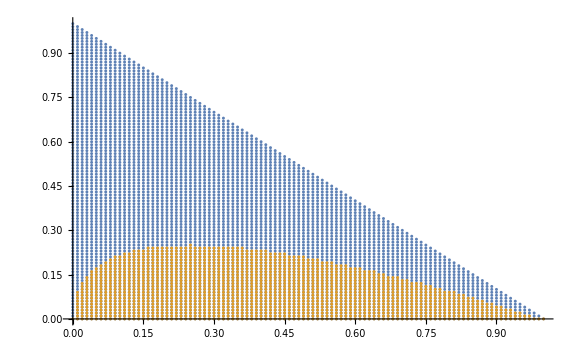

-Graphics3D-

```mathematica
conjecture3 = Select[simplex3,(Sqrt[#[[1]]]*#[[3]])>=#[[2]]&];
difference3 = Union[Complement[rep3,conjecture3],Complement[conjecture3,rep3]]
Row[{ListPointPlot3D[{simplex3,rep3},ImageSize->Large],
ListPointPlot3D[{simplex3,conjecture3},ImageSize->Large]
}]
Row[{ListPlot[{P2[simplex3],P2[rep3]},ImageSize->Large],
ListPlot[{P2[simplex3],P2[conjecture3]},ImageSize->Large]
}]
ListPointPlot3D[difference3,ImageSize->Large,PlotStyle->{Blue,Red},PlotRange->{{0,1},{0,1},{0,1}}]
```

```mathematica
rep4real = Select[simplex4, Representable[#,RealLessThanOneQ]&];
rep4 = Select[simplex4, Representable[#,ProbabilityCoefQ]&];
Row[{ListPointPlot3D[{P3[simplex4],P3[rep4]},ImageSize->Large], ListPointPlot3D[{P3[simplex4],P3[rep4real]},ImageSize->Large]}]
```

-Graphics3D--Graphics3D-

```mathematica
conjecture4=Select[simplex4,(#[[1]]*#[[4]])≥#[[2]]*#[[3]]&];
difference4 = Union[Complement[rep4,conjecture4],Complement[conjecture4,rep4]];
Row[{ListPointPlot3D[{P3[simplex4],P3[rep4]},ImageSize->Large], ListPointPlot3D[{P3[simplex4],P3[conjecture4]},ImageSize->Large]}]
ListPointPlot3D[P3[difference4],ImageSize->Large,PlotStyle->{Blue,Red},PlotRange->{{0,1},{0,1},{0,1}}]
```

-Graphics3D--Graphics3D-

-Graphics3D-

```mathematica
(* Ground PLP represented as list of triples: {prob, variable|Null, variables_list} *)
Restrict[groundPLP_, v1_,v2_] := Select[groundPLP,
With[{head = #⟦2⟧, body=#⟦3⟧},
(head === Null ∨ MemberQ[v1, head]) ∧
SubsetQ[body, v2]
]&
]
Restrict[groundPLP_, i_]:= Restrict[groundPLP,i,i]
```

```mathematica
samplePLP = {{p0,Null, {"a(1)"}}, {p0,Null, {"a(2)"}}, {p1,"a(1)", {"a(2)"}},  {p1,"a(2)", {"a(1)"}}};
Restrict[samplePLP, {"a(1)"}]
RuleProbs[samplePLP]
```

{{p0,Null,{a(1)}}}

{p1,p1}

```mathematica
ComputeP[groundVariables_, groundPLP_, interpretation_]:= 
If[groundVariables == {}, 1,
If[groundVariables == interpretation, 
1 - Sum[ComputeP[groundVariables,groundPLP,i], {i, Subsets[interpretation, Length[interpretation]-1]}],
ComputeP[interpretation,Restrict[groundPLP, interpretation],interpretation] * Product[1-p, {p, #⟦1⟧& /@ Restrict[groundPLP,Complement[groundVariables,interpretation],interpretation]}]
]
]
```

```mathematica
Restrict[samplePLP,{"a(1)"}]
ComputeP[{"a(1)","a(2)"}, samplePLP, {"a(1)","a(2)"}] // FullSimplify
ComputeP[{"a(1)","a(2)"}, samplePLP, {"a(1)"}]
ComputeP[{"a(1)","a(2)"}, samplePLP, {"a(2)"}]
ComputeP[{"a(1)","a(2)"}, samplePLP, {}]
```

{{p0,Null,{a(1)}}}

p0^2-2 (-1+p0) p1-(-1+p0)^2 p1^2

(1-p0) p0 (1-p1)

(1-p0) p0 (1-p1)

(1-p0)^2 (1-p1)^2

```mathematica
Manipulate[ListPlot[{(1-p0)^2 (1-p1)^2, (1-p0) p0 (1-p1), (1-p0) p0 (1-p1),p0^2-2 (-1+p0) p1-(-1+p0)^2 p1^2 }], {p0,0,1},{p1,0,1}]
```